```mathematica
CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
1-2×N[CDF[NormalDistribution[μ,σ],μ-σ]]
```

0.682689

```mathematica
data:={79,141,228,3,20,14,97,194,28,56,75,37,122,27,10,67,23,20,103,11,92,99,64,6,118,136,682,4,70,11,74,40,16,114,8,149,97,7,317,346,188,149,68,150,88,87,155,50,26,143,126,98,153,238,30,53,132,260,296,25,61,87,33,51,74,111,72,178,4,67,43,229,156,117,104,27,23,23,186,524,107,160,41,50,352,8,153,142,306,320,85,44,116,39,264,360,192,142,44,29};
Quartiles[data]
```

{35,87,299/2}

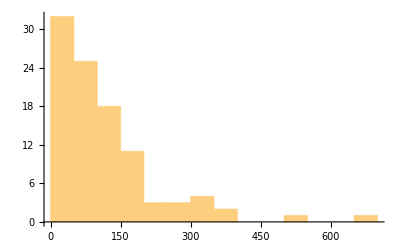

```mathematica
Histogram[data,"FreedmanDiaconis"]
```

```mathematica
Histogram[data,{"Raw","FreedmanDiaconis"}]
```

-Graphics-

```mathematica
CDF[NormalDistribution[0,1],0.24]
```

0.594835

```mathematica
CDF[NormalDistribution[0,1],0.24]-CDF[NormalDistribution[0,1],0]
```

0.0948349

```mathematica
CDF[NormalDistribution[0,1],0.24]-CDF[NormalDistribution[0,1],0.0059]
```

0.0924811

```mathematica
CDF[NormalDistribution[0,1],0.0059]-CDF[NormalDistribution[0,1],0]
```

0.00235375

```mathematica
CDF[NormalDistribution[0,1],1.59]
```

0.944083

```mathematica
CDF[NormalDistribution[0,1],0.68]
```

0.751748

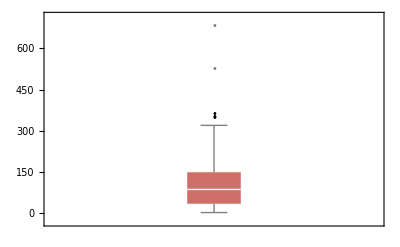

```mathematica
BoxWhiskerChart[data,"Outliers",ChartStyle->56]
```

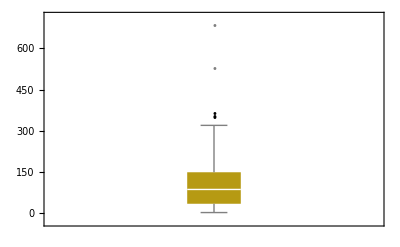

```mathematica
BoxWhiskerChart[data,"Outliers",ChartStyle->50]
```

```mathematica
f[x_]:=x^2;
Integrate[f[x],{x,0,Infinity}]
```

1/3

```mathematica
Integrate[x^2,x]
```

x^3/3

```mathematica
estimatedParameters=FindDistributionParameters[data,NormalDistribution[μ,σ]] (*使用最大似然估计计算参数*)
```

```mathematica
{μ->114.44,σ->112.3624471549723}
```

{μ→114.44,σ→112.362}

```mathematica
Data:={5.8,6.0,7.8,7.4,6.2,6.1,8.6,9.7,4.4,4.4,7.6,9.0,9.2,6.4,7.0,8.7,6.0,6.1,6.8,10.,5.3,8.1,8.9,5.3,6.7,5.6,3.7,8.7,6.6,10.1,6.9,6.6,6.4,5.1};
Mean[Data]
```

6.97647

```mathematica
Variance[Data]
```

2.77822

```mathematica
t=InverseCDF[StudentTDistribution[34-1],1-0.95/2]
```

0.0631855

```mathematica
t=InverseCDF[StudentTDistribution[34-1],1-0.05/2]
```

2.03452

```mathematica
InverseCDF[ChiSquareDistribution[33],0.95]
```

47.3999